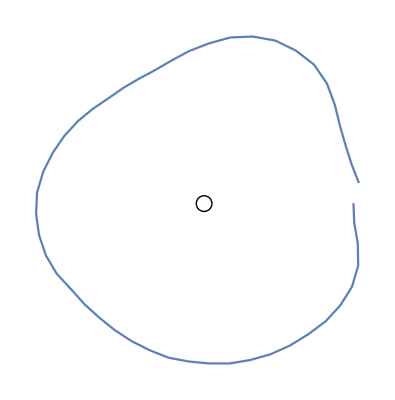

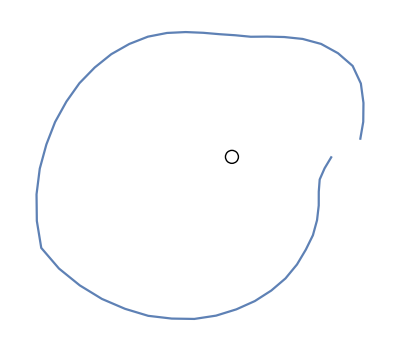

```mathematica
Clear["Global`*"]
x={0,-4.6,-4.3,0,9.2,19.3,26.1,27.5,26.7,21.7,14.1,3.8,-5.2,-13.7,-19.4,-21.1,-20.8,-19.3,-14.3,-8.4,-2.5,3.1,8.7,13.1,14.4,14.1,12.2,8.1,1.8,-0.5,-2.2,-2.1,-1.3,0,2.3,3,4.7,7.3,8.9,11,12.6,14.2,16.9,18,17.5,13,3.6,-6.1,-8.6};

y={0,10,19.5,28.9,33.1,28.6,21.7,11.7,1.2,-7.4,-13.2,-13.2,-10.8,-4.6,4.2,14.6,25,34.1,43.1,51.3,60,68,76.9,85.8,96,106,116,125.3,117.1,106.9,96.9,86.6,77.3,66.5,57.1,46.7,36,26,15.8,5.8,-5.1,-16.1,-25.2,-35.4,-45.6,-54.8,-59.4,-55.3,-45.4};
Array[f,49];
t=Array[#&,49];

xs=Partition[Riffle[t,x],2];
ys=Partition[Riffle[t,y],2];
xy=Partition[Riffle[x,y],2];

baseR=200;
θ=(2π)/49.;
Array[f,49];
θs=Array[θ#&,49];

rs=ConstantArray[baseR,49];
rxCam=rs+x;

xCam=Partition[Riffle[rxCam*Cos[θs],rxCam*Sin[θs]],2];
Show[Graphics[Circle[{0,0},{10,10}]],ListLinePlot[xCam,AspectRatio->1]]

Array[f,49];
θs=Array[θ#&,49];
rs=ConstantArray[baseR,49];
ryCam=rs+y;

yCam=Partition[Riffle[ryCam*Cos[θs],ryCam*Sin[θs]],2];

Show[Graphics[Circle[{0,0},{10,10}]],ListLinePlot[yCam,AspectRatio->1]]
```